# Heat Conduction; numerical solution of steady state problem

## ENGENER201 - Transport Phenomena

Friso Meeusen
12 May 2022

```mathematica
(* This clears all variables and definitions: *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the number of internal celss: *)
n=50;
```

```mathematica
(* This defines a grid with x-coordinates (using spherical coordinates): *)
xgrid=Table[x-(n+1)/2,{n},{x,1,n}];
(* This defines a grid with y-coordinates (using spherical coordinates): *)
ygrid=Table[y-(n+1)/2,{y,1,n},{n}];
```

```mathematica
(* This defines a circle with the center in the middle of the grid and maximum radius: *)
(* This will be our outer circle *)
r=√(xgrid^2+ygrid^2);
outercircle=Map[#≥ (n-1)/2&,r,{2}]/.{True->1,False->0};
(* This defines a circle with the center NOT in the middle of the grid with a small radius: *)
(* This will be our inner cirlce *)
r=√((xgrid-3)^2+ygrid^2);
innercircle=Map[#<3&,r,{2}]/.{True->1,False->0};
```

```mathematica
(* This defines a mask: *)
mask=1-(outercircle+innercircle);
TableForm[mask];
(* This defines the temperature of the innercircle: *)
innercircle*=50;
(* This defines the temperature of the outercircle: *)
outercircle*=10;
```

```mathematica
(* This defines the initial temperature map: *)
Told=innercircle+outercircle;
ArrayPlot[Told,ColorFunction->"TemperatureMap",Axes->True,FrameTicks->Automatic, PlotLegends->Automatic]
```

```mathematica
(* This shows the inital temperature field *)
```

-Graphics-

```mathematica
(* This initializes new field: *)
Tnew=Told;
```

```mathematica
(* This initializes convergence parameter: *)
ϵ=10;
(* This sets the convergence criterion: *)
(* Since the dimensions of the field is rather large, the value of the criterion is increased to reduce computation time.*)
ϵconv=5;
```

```mathematica
(* This calculates new temperature profile: *)
Monitor[
While[ϵ>ϵconv,
Do[
If[mask[[ii,jj]]==1,Tnew[[ii,jj]]=1/4(Told[[ii-1,jj]]+Told[[ii+1,jj]]+Told[[ii,jj-1]]+Told[[ii,jj+1]])];
,{ii,2,n-1},{jj,2,n-1}];
(* This calculates the new convergence: *)
ϵ=N[Total[Abs[Tnew-Told],2]];
(* This replaces the old field with the new field: *)
Told=Tnew;
];
,ProgressIndicator[Dynamic[1/ϵ],{0,1/ϵconv}]]
```

```mathematica
ArrayPlot[Tnew,ColorFunction->"TemperatureMap", PlotLegends->Automatic]
```

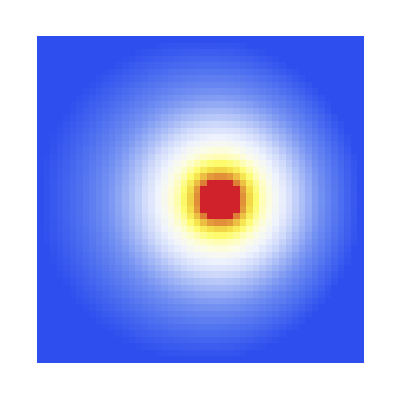

```mathematica
(* This shows the resulting Steady State temperature field*)
```

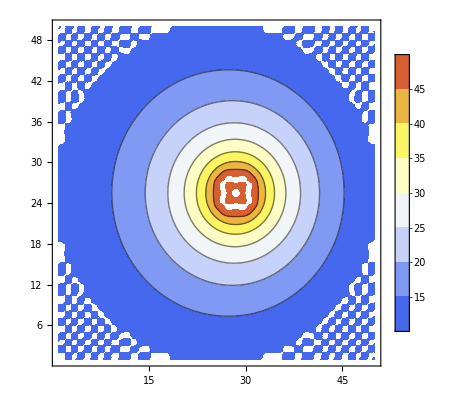

```mathematica
(* This generates a contourplot of the temperature field: *)
(* The origin in a list contourplot is bottom left! *)
ListContourPlot[Tnew,InterpolationOrder->2,Contours->Table[tt,{tt,0,50,5}],
PlotLegends->Automatic,ColorFunction->"TemperatureMap"]
```